```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
$Context
```

Global`

```mathematica
graph = Graph[{{{1,2}},{{2,3}}},{{{0,0}},{{1,1}},{{2,0}}}]
(*ChangeEdges[graph, {{1,3}}]*)
ShowGraph[ graph,VertexLabel->True]
```

Graph[{{{1,2}},{{2,3}}},{{{0,0}},{{1,1}},{{2,0}}}]

ShowGraph[Graph[{{{1,2}},{{2,3}}},{{{0,0}},{{1,1}},{{2,0}}}],VertexLabel→True]

```mathematica
<< GraphPartition`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphPartition`IsoperimetricEdges

Options[IsoperimetricEdges]={RunTwice→False}

GraphPartition`IsoperimetricEdges

Options[GraphPartition`IsoperimetricEdges]={GraphPartition`RunTwice→False}

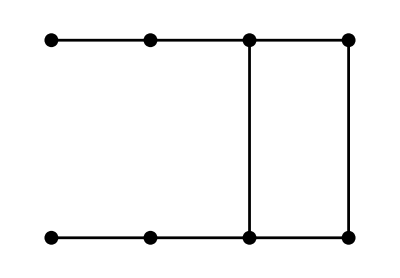

```mathematica
?GraphPartition`IsoperimetricEdges
ShowGraph[RoachGraph[4]]
```

```mathematica
(*Import["GraphPartition.m"]
<<GraphPartition`*)
ga=RoachGraph[4];
(*<< Combinatorica`
*)ShowGraph[ga]
(*VectorCut[ga]
CriterionCut[ga,{1,2,0}]
*)
(*ShowSpectralCut[ga]
*)
```

-Graphics-

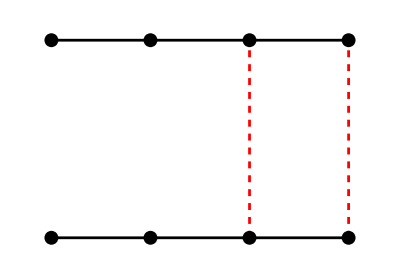

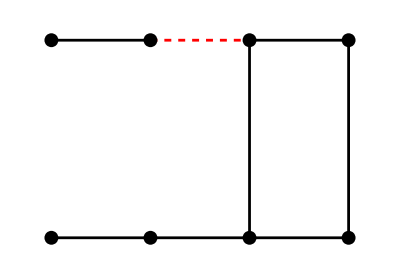

```mathematica
GraphPartition`ShowSpectralCut[ga]
GraphPartition`ShowIsoperimetricCut[SetVertexWeights[ga,Table[1,8]]]
```

```mathematica
?GraphPartition`SpectralCut
?GraphPartition`IsoperimetricEdges
```

SpectralCut[g] returns the result of partitioning the graph into
	two graphs, or rather two disconnected components of a single
	Mathematica graph.

GraphPartition`IsoperimetricEdges

GraphPartition`IsoperimetricEdges[GraphPartition`g_GraphPartition`Graph,OptionsPattern[]]:=With[{GraphPartition`v=IsoperimetricVector[GraphPartition`g,GraphPartition`Substitutions→Sort[(#1⟦Random[Integer,{2,Length[#1]}]⟧&)/@System`ConnectedComponents[GraphPartition`g]],GraphPartition`IsoperimetricMode→If[OptionValue[GraphPartition`RunTwice],GraphPartition`Twice,GraphPartition`Fixed]]},VectorCut[GraphPartition`g,GraphPartition`v,CriterionCut[GraphPartition`g,GraphPartition`v]]]
 
Options[GraphPartition`IsoperimetricEdges]={GraphPartition`RunTwice→False}

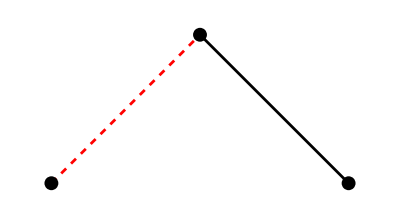

```mathematica
ShowSpectralCut[⁃Graph:<2,3,Undirected>⁃]
```

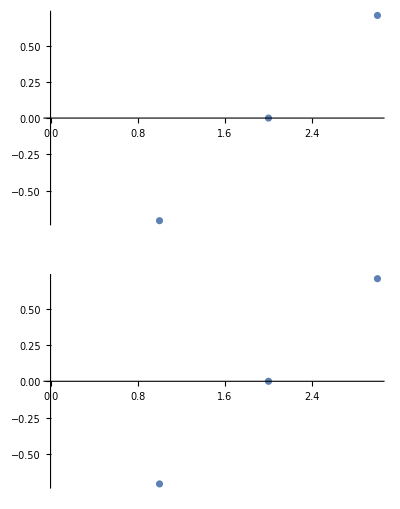

```mathematica
PlotFiedlerVector[ga]
```

```mathematica
Edges[ga]
Complement[Edges[ga],SpectralEdges[ga]]
SpectralEdges[ga]
ShowSpectralCut[ga]
```

{{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{3,7},{4,8}}

{{1,2},{2,3},{3,4},{5,6},{6,7},{7,8}}

{{3,7},{4,8}}

-Graphics-

```mathematica
FiedlerVector[ga]
```

{-0.567175,-0.402283,-0.120438,-0.0444539,0.567175,0.402283,0.120438,0.0444539}

```mathematica
Eigensystem[N[LaplacianMatrix[ga]]]
Thread[Apply[List,Eigensystem[N[LaplacianMatrix[ga]]]]]
```

{{4.90321,3.41421,2.80606,2.,2.,0.585786,0.290725,-1.38778×10^-16},{{-0.0572688,0.223532,-0.591693,0.310892,0.0572688,-0.223532,0.591693,-0.310892},{-0.191342,0.46194,-0.46194,0.191342,-0.191342,0.46194,-0.46194,0.191342},{0.223681,-0.403982,0.101954,0.525709,-0.223681,0.403982,-0.101954,-0.525709},{0.477593,-0.477593,-0.477593,0.148003,0.148003,-0.148003,-0.148003,0.477593},{-0.148003,0.148003,0.148003,0.477593,0.477593,-0.477593,-0.477593,-0.148003},{-0.46194,-0.191342,0.191342,0.46194,-0.46194,-0.191342,0.191342,0.46194},{-0.567175,-0.402283,-0.120438,-0.0444539,0.567175,0.402283,0.120438,0.0444539},{-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553}}}

{{4.90321,{-0.0572688,0.223532,-0.591693,0.310892,0.0572688,-0.223532,0.591693,-0.310892}},{3.41421,{-0.191342,0.46194,-0.46194,0.191342,-0.191342,0.46194,-0.46194,0.191342}},{2.80606,{0.223681,-0.403982,0.101954,0.525709,-0.223681,0.403982,-0.101954,-0.525709}},{2.,{0.477593,-0.477593,-0.477593,0.148003,0.148003,-0.148003,-0.148003,0.477593}},{2.,{-0.148003,0.148003,0.148003,0.477593,0.477593,-0.477593,-0.477593,-0.148003}},{0.585786,{-0.46194,-0.191342,0.191342,0.46194,-0.46194,-0.191342,0.191342,0.46194}},{0.290725,{-0.567175,-0.402283,-0.120438,-0.0444539,0.567175,0.402283,0.120438,0.0444539}},{-1.38778×10^-16,{-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553,-0.353553}}}

```mathematica
List[1,2,3,4]
```

{1,2,3,4}

```mathematica
Thread[Apply[List, {{1,2,3,4},{0,1,2,3}}]]
```

{{1,0},{2,1},{3,2},{4,3}}

```mathematica
List[{1,2,3,4},True]
```

{{1,2,3,4},True}

```mathematica
Edges[ga]
```

{{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{3,7},{4,8}}

```mathematica
IsoperimetricVector[ga]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Map[ #[[Random[Integer,{1,Length[#]}]]]&, ConnectedComponents[ga]]
```

```mathematica
MatrixForm[LaplacianMatrix[ga]]
MatrixForm[RowColumnDrop[LaplacianMatrix[ga],{{1,2}}]]
```

(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 3 | -1 | 0 | 0 | -1 | 0
0 | 0 | -1 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 0 | 0 | -1 | 3 | -1
0 | 0 | 0 | -1 | 0 | 0 | -1 | 2)

Delete::partw: Part 2 of {1,0,0,0,0,0,0} does not exist.

Delete::partw: Part 2 of {-1,2,-1,0,0,0,0,0} does not exist.

Delete::partw: Part 2 of {0,-1,3,-1,0,0,-1,0} does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

(Delete[{1,0,0,0,0,0,0},{{1,2}}]
Delete[{-1,2,-1,0,0,0,0,0},{{1,2}}]
Delete[{0,-1,3,-1,0,0,-1,0},{{1,2}}]
Delete[{0,0,-1,2,0,0,0,-1},{{1,2}}]
Delete[{0,0,0,0,1,-1,0,0},{{1,2}}]
Delete[{0,0,0,0,-1,2,-1,0},{{1,2}}]
Delete[{0,0,-1,0,0,-1,3,-1},{{1,2}}]
Delete[{0,0,0,-1,0,0,-1,2},{{1,2}}])

```mathematica
MatrixForm[{{2,-1,0,0,0,0,0},{-1,3,-1,0,0,-1,0},{0,-1,2,0,0,0,-1},{0,0,0,1,-1,0,0},{0,0,0,-1,2,-1,0},{0,-1,0,0,-1,3,-1},{0,0,-1,0,0,-1,2}}]
```

(2 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 3 | -1 | 0 | 0 | -1 | 0
0 | -1 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0
0 | -1 | 0 | 0 | -1 | 3 | -1
0 | 0 | -1 | 0 | 0 | -1 | 2)

```mathematica
MatrixForm[{{2,-1,0,0,0,0,0},{-1,3,-1,0,0,-1,0},{0,-1,2,0,0,0,-1},{0,0,0,1,-1,0,0},{0,0,0,-1,2,-1,0},{0,-1,0,0,-1,3,-1},{0,0,-1,0,0,-1,2}}]
```

(2 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 3 | -1 | 0 | 0 | -1 | 0
0 | -1 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0
0 | -1 | 0 | 0 | -1 | 3 | -1
0 | 0 | -1 | 0 | 0 | -1 | 2)

4

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of sth$132921+1.

Hold[sth$132921+1]

```mathematica
sth
```

sth

```mathematica
other
```

other

```mathematica
subs=Sort[Map[ #[[Random[Integer,{1,Length[#]}]]]&, ConnectedComponents[ga]]]
```

{3}

```mathematica
MatrixForm[LaplacianMatrix[ga]]
MatrixForm[RowColumnDrop[LaplacianMatrix[ga],{{3},{1}}]]
```

(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 3 | -1 | 0 | 0 | -1 | 0
0 | 0 | -1 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 0 | 0 | -1 | 3 | -1
0 | 0 | 0 | -1 | 0 | 0 | -1 | 2)

(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | -1
0 | 0 | 1 | -1 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | -1 | 3 | -1
0 | -1 | 0 | 0 | -1 | 2)

```mathematica
MatrixForm[{{1,-1,0,0,0,0,0},{-1,2,0,0,0,0,0},{0,0,2,0,0,0,-1},{0,0,0,1,-1,0,0},{0,0,0,-1,2,-1,0},{0,0,0,0,-1,3,-1},{0,0,-1,0,0,-1,2}}]
```

(1 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | -1 | 3 | -1
0 | 0 | -1 | 0 | 0 | -1 | 2)

```mathematica
GetVertexWeights[ga][[1]]=1
```

Set::setps: GetVertexWeights[ga] in the part assignment is not a symbol.

1

```mathematica
ga[[VetexWeights]]
```

Part::pkspec1: The expression VetexWeights cannot be used as a part specification.

(⁃Graph:<8,8,Undirected>⁃)⟦VetexWeights⟧

```mathematica
ga = SetVertexWeights[ga,Table[1,8]]
```

⁃Graph:<8,8,Undirected>⁃

```mathematica
GetVertexWeights[ga]
```

{0,0,0,0,0,0,0,0}

```mathematica
Table[1,8]
```

{1,1,1,1,1,1,1,1}

```mathematica
v=IsoperimetricVector[ga,
			Substitutions->{1},IsoperimetricMode->Fixed]
```

{1,0.866667,0.8,0.2,0.466667,0,0.266667,0.4}

```mathematica
Import["GraphPartition.m","Package"]
```

```mathematica
Import["GraphPartition.m"]
<< GraphPartition`
<< Combinatorica`
ShowGraph[ga]
IsoperimetricEdges[ga]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

-Graphics-

VectorCut[⁃Graph:<8,8,Undirected>⁃,IsoperimetricVector[⁃Graph:<8,8,Undirected>⁃,{7},IsoperimetricMode→Fixed],CriterionCut[⁃Graph:<8,8,Undirected>⁃,IsoperimetricVector[⁃Graph:<8,8,Undirected>⁃,{7},IsoperimetricMode→Fixed]]]

```mathematica
?GraphPartition`IsoperimetricEdges
```

GraphPartition`IsoperimetricEdges

Options[IsoperimetricEdges]={RunTwice→False}

ShowGraph[⁃Graph:<8,8,Undirected>⁃]